```mathematica
lower = -1;
upper = 1;

EV[x_] = Integrate[x * (1/2(1 - x * x)), {x, lower, upper}] 
V[x_] = Integrate[Integrate[(x^2 * (1 - x^2 * x^2)), {x, lower ,upper}], {x, lower, upper}]
```

0

16/21

```mathematica
(* Does the scaled Epanechnikov Kernel integrate to one?*)
```

4/(√21)

1

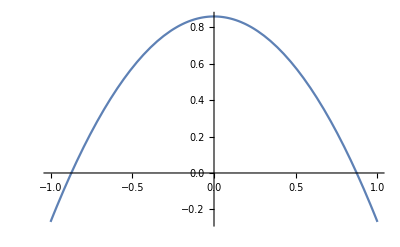

```mathematica
dim = 1;
v = 16/21;
boundary = √v
lower = - 1 * boundary;
upper = + 1 * boundary;
Subscript[c, d] = 2/dim * Pi^(dim/2)/Gamma[dim/2];
kernel = (2 + dim)/(2 * Subscript[c, d])* (1/(√v))* (1 - 1/v(x^2));
Integrate[kernel, {x, lower, upper}]
Plot[kernel, {x, -1, 1}, GridLines->{{lower, upper}, {0,1}}]
```

```mathematica
(* Compute the integral of the 'normal' Epanechnikov kernel *)
```

```mathematica
kernel = (2 + dim)/(2 * Subscript[c, d])* (1 -x^2);
Integrate[kernel, {x, -1, 1}]
```

1